MÉTODO DE NEWTON-RAPHSON

EJEMPLO

```mathematica
f[x_]:= -x^4+6 x^2+11;
```

```mathematica
y[x_,a_]:=d[a](x-a)+f[a];
```

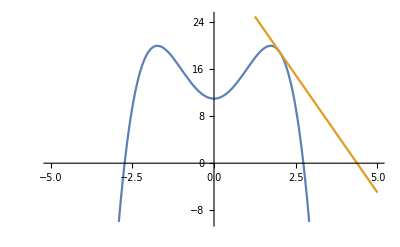

```mathematica
Plot[{f[x],y[x,2]},{x,-5,5},PlotRange->{-10,25}]
```

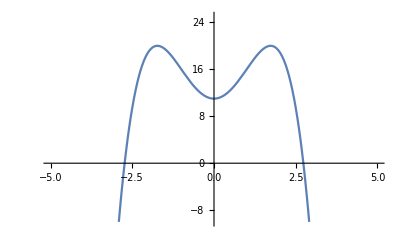

```mathematica
Plot[f[x],{x,-5,5}, PlotRange->{-10,25}]
```

```mathematica
D[f[x],x]
```

12 x-4 x^3

```mathematica
d[x_]:=12 x-4 x^3;
```

```mathematica
x[0]=20;
```

```mathematica
x[n_]:=x[n-1]- f[x[n-1]]/d[x[n-1]];
```

```mathematica
e[n_]:= Abs[x[n]-x[n-1]];
```

```mathematica
m = N[Table[{n,x[n],e[n],TrueQ[e[n]<10^-6]},{n,1,25}]];
```

$Aborted

```mathematica
Insert[
Grid[Prepend[m,{"n","x_n","e_n","e_n<10^-6"}],Frame->All],Alignment->Left,2]
```

n | x_n | e_n | e_n<10^-6
1. | 4.375 | 2.375 | False
2. | 3.52348 | 0.851515 | False
3. | 3.00619 | 0.517291 | False
4. | 2.77963 | 0.226566 | False
5. | 2.73513 | 0.0444949 | False
6. | 2.73352 | 0.00160993 | False
7. | 2.73352 | 2.06019×10^-6 | False
8. | 2.73352 | 3.37067×10^-12 | True